# Decision boundary

```mathematica
f[fbase_, steps_, L_, r_, delta_] = (L - 1 - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(L - t),{t, 1,steps}])
```

9

10

{{1,0.988806,0.979581,0.972222,0.966556,0.962365,0.959418,0.957492,0.95638,0.955901},{1,0.977612,0.959161,0.944444,0.933111,0.924729,0.918836,0.914984,0.91276,0.911801},{1,0.966418,0.938742,0.916667,0.899667,0.887094,0.878255,0.872476,0.86914,0.867702},{1,0.955224,0.918322,0.888889,0.866223,0.849458,0.837673,0.829968,0.82552,0.823603}}

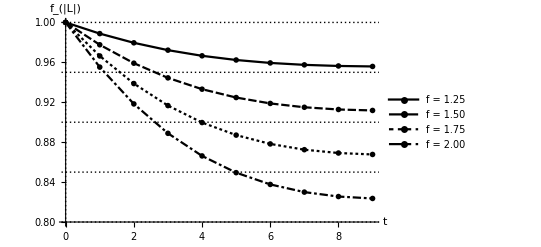

{1,0.998756,0.998205,0.997965,0.997864,0.997822,0.997805,0.997799,0.997797,0.997796}

```mathematica
time = 9
layers = 10
data = Table[Prepend[f[x,time,layers,0.05,0.9],1], {x,1.25,2.0,0.25}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {0.8, 1}, AxesLabel->{"t", "f_(|L|)"}, PlotLegends->{"f = 1.25", "f = 1.50", "f = 1.75", "f = 2.00"}, GridLines->{{0}, {0.8, 0.85, 0.9, 0.95, 1.0}}, DataRange->{0, time}]
```